```mathematica
(*Code was created by Loïc Marrec*)
```

```mathematica
(*Description:Fixation time in the island model*)
```

```mathematica
(*PARAMETERS*)
```

```mathematica
bW=1; (*Wild-type birth rate*)
```

```mathematica
dW=0.1; (*Wild-type death rate*)
```

```mathematica
bM=Table[i,{i,0.95,1.1,0.001}]; (*Mutant birth rate range*)
```

```mathematica
dM=0.1; (*Mutant death rate*)
```

```mathematica
Δ=5; (*Number of demes*)
```

```mathematica
κ=100; (*Carrying capacity per deme*)
```

```mathematica
(*EQUILIBRIUM DEME SIZES*)
```

```mathematica
NW=κ*(1-dW/bW); (*Wild-type deme equilibrium size*)
```

```mathematica
NM=Table[κ*(1-dM/bM[[i]]),{i,1,Length[bM]}]; (*Mutant deme equilibrium sizes*)
```

```mathematica
(*FIXATION PROBABILITIES WITHIN DEMES*)
```

```mathematica
uW=Table[If[bM[[i]]==bW*dM/dW,1/NM[[i]],(1-Exp[-Log[bW*dM/(dW*bM[[i]])]])/(1-Exp[-NM[[i]]*Log[bW*dM/(dW*bM[[i]])]])],{i,1,Length[bM]}]; (*Fixation probability of a wild type in a mutant deme*)
```

```mathematica
uM=Table[If[bM[[i]]==bW*dM/dW,1/NW,(1-Exp[-Log[bM[[i]]*dW/(dM*bW)]])/(1-Exp[-NW*Log[bM[[i]]*dW/(dM*bW)]])],{i,1,Length[bM]}];
(*Fixation probability of a mutant in a wild-type deme*)
```

```mathematica
(*DISPERSAL PARAMETERS*)
```

```mathematica
mM={0.000001,0.000001,0.000001,0.000002,0.000005}; (*Mutant dispersal rates*)
```

```mathematica
mW={0.000005,0.000002,0.000001,0.000001,0.000001};(*Wild-type dispersal rates*)
```

```mathematica
α=mM/mW;(*Ratio of dispersal rates*)
```

```mathematica
(*RELATIVE FITNESS BETWEEN DEMES*)
```

```mathematica
r=Table[α[[j]]*(NM[[i]]*uM[[i]])/(NW*uW[[i]]),{i,Length[bM]},{j,1,Length[α]}];
```

```mathematica
(*GLOBAL FIXATION TIME CALCULATION*)
```

```mathematica
tfix=Table[If[r[[i,j]]==1,(*Neutral case*)(-1+Δ)^2/(mM[[j]]*NM[[i]]*uM[[i]]*Δ),(*Selection case*)(-1+Δ)*(1/(1-r[[i,j]]^-Δ))*(1/(mM[[j]]*NM[[i]]*uM[[i]]))*Sum[Sum[(r[[i,j]]^(l-k)-r[[i,j]]^-k)/(l*(Δ-l)),{l,1,k}],{k,1,Δ-1}]],{i,Length[bM]},{j,1,Length[α]}];
```

```mathematica
(*DATA PREPARATION AND VISUALIZATION*)
```

```mathematica
tfixtable=Table[{bM[[j]]/bW-1,tfix[[j,i]]},{i,1,Length[α]},{j,1,Length[bM]}]; (*Selection coefficient vs.fixation time*)
```

```mathematica
colorRain=Table[ColorData["Rainbow"][k],{k,0,1,1/(Length[α]-1)}]; (*Color gradient for plots*)
```

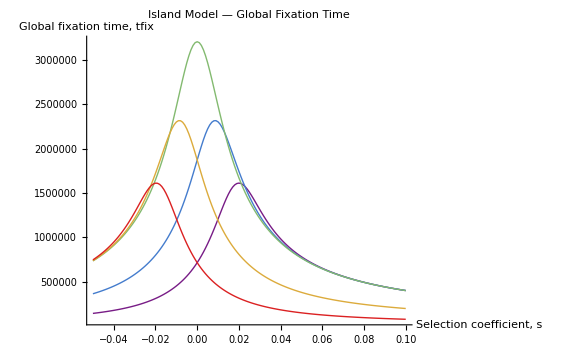

```mathematica
Show[Table[ListPlot[tfixtable[[f]],PlotStyle->{colorRain[[f]],Thick},Joined->True],{f,1,Length[α]}],PlotLabel->"Island Model — Global Fixation Time",PlotRange->All,AxesLabel->{"Selection coefficient, s","Global fixation time, tfix"},ImageSize->Large]
```